```mathematica
success=ReadList["C:\\Users\\Christopher Plumberg\\Downloads\\success_sph.dat",Real];
fail=ReadList["C:\\Users\\Christopher Plumberg\\Downloads\\error_sph.dat",Real];
success=ArrayReshape[success,{Length[success]/6,6}];
fail=ArrayReshape[fail,{Length[fail]/6,6}];
```

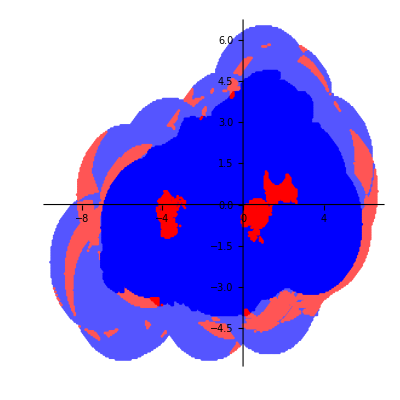

```mathematica
eFO=0.266112;
ListPlot[{(Select[success,#[[3]]<eFO&])[[;;,{1,2}]],(Select[fail,#[[3]]<eFO&])[[;;,{1,2}]],(Select[success,#[[3]]≥eFO&])[[;;,{1,2}]],(Select[fail,#[[3]]≥eFO&])[[;;,{1,2}]]},PlotStyle->{{PointSize[0.005],Blue//Lighter},{PointSize[0.005],Red//Lighter},{PointSize[0.005],Blue},{PointSize[0.005],Red}},AspectRatio->1]
```